{-5,-4,-3,-2,-1,0,1,2,3,4,5}

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

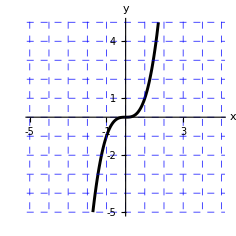

```mathematica
Clear[f,x];

f[x_] :=x^3/;-6≤x<6;

xTicks=Table[n ,{n,-5,5}]
yTicks=Table[n,{n,-5,5}]
One=Plot[f[x],{x,-5,5},PlotRange->{-5,5},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.009]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4,-3, -2,-1,0,1,2,3,4,5},{-5,-4,-3, -2,-1,0,1,2,3,4,5}},GridLinesStyle-> Directive[Blue,Dashed]]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

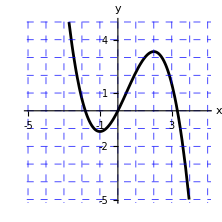

```mathematica
Clear[f,x];

f[x_] :=-x^3/3+x^2/2+2x/;-6≤x<6;

xTicks=Table[n ,{n,-5,5}]
yTicks=Table[n,{n,-5,5}]
One=Plot[f[x],{x,-5,5},PlotRange->{-5,5},Ticks->{xTicks,yTicks},
    PlotStyle->{{Black,Thickness[0.009]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4,-3, -2,-1,0,1,2,3,4,5},{-5,-4,-3, -2,-1,0,1,2,3,4,5}},GridLinesStyle-> Directive[Blue,Dashed]]
```